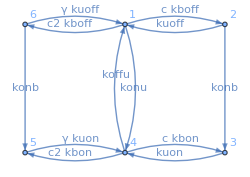

```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica-nbs"];
Get["ctmc`"]
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},
	    {4,5},{5,4},{6,5},{4,1},{2,3},{1,4}};
weights2={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F31 = Fon[[3,1]][[1]];
F41 = Fon[[4,1]][[1]];
F51 = Fon[[5,1]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {6,1,2};
onStates = {5,4,3};
Foff1on = LaplaceTransformToSetByState[Q2,1,onStates,s1];
FoffOn = Foff1on[[3]][[1]]*F31 +Foff1on[[2]][[1]]*F41 + Foff1on[[1]][[1]]*F51; (*F1off[[2]][[1]]*F41 +*)
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];
```

```mathematica
meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];
```

```mathematica
τfun[c_,c2_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_ ]:=Evaluate[τ];
τNum[c_?NumericQ,c2_?NumericQ,γ_?NumericQ,kboff_?NumericQ,konb_?NumericQ,kuon_?NumericQ,kbon_?NumericQ,koffu_?NumericQ,kuoff_?NumericQ,konu_?NumericQ]:=Evaluate[τ];
```

```mathematica
ClearAll[Pjoint];
ClearAll[d2LogPjoint];
ClearAll[integrand];
ClearAll[expr1];
ClearAll[expr2];
ClearAll[exprS1];
ClearAll[exprS12];

expr1 = FoffOn /.{γ->1};
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Apart[exprS1,s2];

(*Joint PDF of ON/OFF durations*)
Pjoint=InverseLaplaceTransform[exprS12,{s1,s2},{t1,t2},Assumptions->assum];
d2LogPjoint =D[Log[Pjoint],{c,2}];
integrand = Pjoint *d2LogPjoint ;
```

```mathematica
(*Checking that ILT ran correctly*)
PjointSimpl=Simplify[Pjoint,{A==(c kboff+c2 kboff+konb+konu+kuoff)^2-4 (c kboff konb+c2 kboff konb+konu (konb+kuoff)),B==c kbon+c2 kbon+koffu+kuon,D==-4 koffu kuon+(c kbon+c2 kbon+koffu+kuon)^2}]
```

1/(4 √A √D)ⅇ^(-1/2 (√A+c kboff+c2 kboff+konb+konu+kuoff) t1-1/2 (B+√D) t2) koffu (√A (1+ⅇ^(√A t1)) konu (B-B ⅇ^(√D t2)+√D (1+ⅇ^(√D t2))+2 (-1+ⅇ^(√D t2)) kuon)+(-1+ⅇ^(√A t1)) (-c2 √D kboff konu-c2 √D ⅇ^(√D t2) kboff konu-c √D (1+ⅇ^(√D t2)) kboff konu+√D konb konu+√D ⅇ^(√D t2) konb konu-√D konu^2-√D ⅇ^(√D t2) konu^2+B (-1+ⅇ^(√D t2)) konu (c kboff+c2 kboff-konb+konu-kuoff)+√D konu kuoff+√D ⅇ^(√D t2) konu kuoff-4 c2 kboff konb kuon+4 c2 ⅇ^(√D t2) kboff konb kuon+2 c (-1+ⅇ^(√D t2)) kboff (2 konb-konu) kuon+2 c2 kboff konu kuon-2 c2 ⅇ^(√D t2) kboff konu kuon-2 konb konu kuon+2 ⅇ^(√D t2) konb konu kuon+2 konu^2 kuon-2 ⅇ^(√D t2) konu^2 kuon-2 konu kuoff kuon+2 ⅇ^(√D t2) konu kuoff kuon))

```mathematica
(*Compiling the integrand*)
ClearAll[integrandC];
integrandC=Compile[{{c,_Real},{c2,_Real},{t1,_Real},{t2,_Real},{kboff,_Real},{konb,_Real},{kuon,_Real},{kbon,_Real},{koffu,_Real},{kuoff,_Real},{konu,_Real}},
Evaluate[integrand],
CompilationTarget->"C",
RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
(*Adding numerical guards*)
ClearAll[integrandCNum];
integrandCNum[c_?NumericQ,c2_?NumericQ,t1_?NumericQ,t2_?NumericQ,kboff_?NumericQ,konb_?NumericQ,kuon_?NumericQ,kbon_?NumericQ,koffu_?NumericQ,kuoff_?NumericQ,konu_?NumericQ]:=integrandC[N[c],N[c2],N[t1],N[t2],N[kboff],N[konb],N[kuon],N[kbon],N[koffu],N[kuoff],N[konu]];
(*Check*)
(*integrandCNum[__]:=0.;*)
integrandCNum[1,1,1,1,1,1,1,1,1,1,1]
```

0.00346896

```mathematica
(*Numerically integrating for the Fisher info rate*)
kmin =0.001;
kmax = 5.;
kdl=0.0888;
c0=40.;
ω=1.;
cw=ω*c0;
γ=1.;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0]];

integral=-NIntegrate[integrandCNum[c0,cw,t1,t2,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin],{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->0}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->10];
integral*c0^2/τfun[c0,cw,γ,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.154752

```mathematica
ClearSystemCache[]
```

```mathematica
(*Wrapping it into a function*)
ClearAll[FisherFast];
ClearAll[FisherSafe];

FisherFast[c0i_?NumericQ,c2i_?NumericQ,γi_?NumericQ,kboffi_?NumericQ,konbi_?NumericQ,kuoni_?NumericQ,kboni_?NumericQ,koffui_?NumericQ,kuoffi_?NumericQ,konui_?NumericQ ]:=Module[{τPartialEval,integral},
τPartialEval=τNum[c0i,c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui];
integral=-NIntegrate[integrandCNum[c0i,c2i,t1,t2,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui],{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->0}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->6];
integral*c0i^2/τPartialEval];

FisherSafe[pars__?NumericQ]:=
Quiet[
Check[
FisherFast[pars],
-1,(* ← penalty when NIntegrate fails*)
{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
],{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
];
```

```mathematica
(*Check*)
cvals=10^Range[-1.,2.,3/41];
kmin =0.0001;
kmax = 5.;
kdl=0.0888;
c0=50.;
ω=10.;
cw=ω*c0;
γ=1.;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0]];
FisherSafe[c0,cw,γ,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.155358

```mathematica
CloseKernels[];
```

```mathematica
ParallelKernels[]
```

```mathematica
LaunchKernels[14];                       (*ensure you actually have sub-kernels running*)
DistributeDefinitions[integrandC,integrandCNum,FisherFast,FisherSafe,cvals,kmin,kmax,kdl,ω,γ];
```

```mathematica
(*Maximize*)

Now
results=
ParallelTable[
Reap[
NMaximize[
{FisherSafe[cvals[[i]],ω*cvals[[i]],γ,kboff,kmax,kmax,kbon,kmax,kuoff,konu],
kmin<=kboff<=kdl,
kmin<=kbon<=kdl,
kmin<=kuoff<=kmax,
kmin<=konu<=kmax},
{kboff,kbon,kuoff,konu},
Method->"NelderMead",
PrecisionGoal->3,AccuracyGoal->3,MaxIterations->5,
StepMonitor:>Print["Rates = ",{kboff,kbon,kuoff,konu}],
EvaluationMonitor:>Sow[{kboff,kbon,kuoff,konu}]
]
],{i,1,42},
Method->"CoarsestGrained"
];
Now

(*Saving data*)
dir = ".julia/dev/LLROpt/mathematica-nbs";
datadir = FileNameJoin[dir,"data"];
plotdir = FileNameJoin[dir,"plots"];
date = "20250503";
fname10 = "max-F-vs-c-w-10-g-1.wl";
(*fname01 = "max-F-vs-c-w-0.1-g-1.wl";
fname1 = "max-F-vs-c-w-1-g-1.wl";
datafile01 = FileNameJoin[{$HomeDirectory},datadir, date, fname01];
datafile1 = FileNameJoin[{$HomeDirectory},datadir, date, fname1];*)
datafile10 = FileNameJoin[{$HomeDirectory},datadir, date, fname10];
Save[datafile10,results]
```

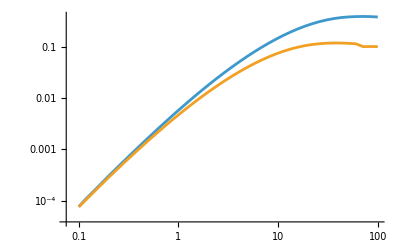

```mathematica
(*Plot*)
ClearAll[results1];
ClearAll[results01];
results01 = Get[datafile01];
results1 = Get[datafile1];
ListLinePlot[{Table[{cvals[[i]],results01[[i]][[1]][[1]]},{i,1,42}],Table[{cvals[[i]],results1[[i]][[1]][[1]]},{i,1,42}]},
ScalingFunctions->{"Log","Log"}]
```